# Hybrid Astronomical Image Processing with Python and WL

## Tom Sherlock, Wolfram Research, Inc.

## #WolframTechConf

## ABSTRACT

Mathematica’s powerful astronomical image processing capabilities can be further enhanced by taking advantage of built-in Python interoperability.

## Why use Python?

Alignment of star fields works best with an algorithm tailored for the point-source data of star fields.  Our native image alignment routines are more general.

I could have re-coded the algorithm in WL, but it was already present as a Python module and Mathematica can use Python seamlessly.

Keeping parts of the pipeline in separate processes, reduces Mathematica memory load.

Reference:

Astroalign: A Python module for astronomical image registration. Beroiz, M., Cabral, J. B., & Sanchez, B. Astronomy and Computing, Volume 32, July 2020, 100384.

https://www.sciencedirect.com/science/article/pii/S221313372030038X

## Python Prerequisites

install python and pip3 for your system
I used python 3.9

### From command line:

pip3 install astroalign
pip3 install astropy

### From inside Mathematica:

```mathematica
FindExternalEvaluators["Python"]
```

```mathematica
python="C:\\Users\\tom\\AppData\\Local\\Programs\\Python\\Python39\\python.exe"
FileExistsQ[python] (*this should verify the executable exists if not use correct python executable*)
```

C:\Users\tom\AppData\Local\Programs\Python\Python39\python.exe

True

```mathematica
RunProcess[{python,"-m","pip","install","--user","astropy"}]
```

<|ExitCode→0,StandardOutput→Collecting astropy\r
  Using cached astropy-4.3.1-cp39-cp39-win_amd64.whl (6.4 MB)\r
Collecting pyerfa>=1.7.3\r
  Using cached pyerfa-2.0.0-cp39-cp39-win_amd64.whl (366 kB)\r
Collecting numpy>=1.17\r
  Using cached numpy-1.21.2-cp39-cp39-win_amd64.whl (14.0 MB)\r
Installing collected packages: numpy, pyerfa, astropy\r
Successfully installed astropy-4.3.1 numpy-1.21.2 pyerfa-2.0.0\r
,StandardError→  WARNING: The script f2py.exe is installed in 'C:\Users\tom\AppData\Roaming\Python\Python39\Scripts' which is not on PATH.\r
  Consider adding this directory to PATH or, if you prefer to suppress this warning, use --no-warn-script-location.\r
  WARNING: The scripts fits2bitmap.exe, fitscheck.exe, fitsdiff.exe, fitsheader.exe, fitsinfo.exe, samp_hub.exe, showtable.exe, volint.exe and wcslint.exe are installed in 'C:\Users\tom\AppData\Roaming\Python\Python39\Scripts' which is not on PATH.\r
  Consider adding this directory to PATH or, if you prefer to suppress this warning, use --no-warn-script-location.\r
WARNING: You are using pip version 21.2.2; however, version 21.2.4 is available.\r
You should consider upgrading via the 'C:\Users\tom\AppData\Local\Programs\Python\Python39\python.exe -m pip install --upgrade pip' command.\r
|>

```mathematica
RunProcess[{python,"-m","pip","install","--user","astroalign"}]
```

<|ExitCode→0,StandardOutput→Collecting astroalign\r
  Using cached astroalign-2.4.tar.gz (57 kB)\r
Requirement already satisfied: numpy>=1.11 in c:\users\tom\appdata\roaming\python\python39\site-packages (from astroalign) (1.21.2)\r
Collecting scipy>=0.15\r
  Using cached scipy-1.7.1-cp39-cp39-win_amd64.whl (33.8 MB)\r
Collecting scikit-image\r
  Using cached scikit_image-0.18.3-cp39-cp39-win_amd64.whl (12.2 MB)\r
Collecting sep\r
  Using cached sep-1.2.0-cp39-cp39-win_amd64.whl (211 kB)\r
Collecting imageio>=2.3.0\r
  Using cached imageio-2.9.0-py3-none-any.whl (3.3 MB)\r
Collecting pillow!=7.1.0,!=7.1.1,>=4.3.0\r
  Using cached Pillow-8.3.2-cp39-cp39-win_amd64.whl (3.2 MB)\r
Collecting networkx>=2.0\r
  Using cached networkx-2.6.3-py3-none-any.whl (1.9 MB)\r
Collecting matplotlib!=3.0.0,>=2.0.0\r
  Using cached matplotlib-3.4.3-cp39-cp39-win_amd64.whl (7.1 MB)\r
Collecting PyWavelets>=1.1.1\r
  Using cached PyWavelets-1.1.1-cp39-cp39-win_amd64.whl (4.2 MB)\r
Collecting tifffile>=2019.7.26\r
  Using cached tifffile-2021.8.30-py3-none-any.whl (171 kB)\r
Collecting kiwisolver>=1.0.1\r
  Using cached kiwisolver-1.3.2-cp39-cp39-win_amd64.whl (52 kB)\r
Collecting cycler>=0.10\r
  Using cached cycler-0.10.0-py2.py3-none-any.whl (6.5 kB)\r
Collecting python-dateutil>=2.7\r
  Using cached python_dateutil-2.8.2-py2.py3-none-any.whl (247 kB)\r
Collecting pyparsing>=2.2.1\r
  Using cached pyparsing-2.4.7-py2.py3-none-any.whl (67 kB)\r
Collecting six\r
  Using cached six-1.16.0-py2.py3-none-any.whl (11 kB)\r
Building wheels for collected packages: astroalign\r
  Building wheel for astroalign (setup.py): started\r
  Building wheel for astroalign (setup.py): finished with status 'done'\r
  Created wheel for astroalign: filename=astroalign-2.4-py3-none-any.whl size=14368 sha256=6737d02d64c29b43b3ef4502c38a5d71258910a1bc1bba843d0281513cd9e07b\r
  Stored in directory: c:\users\tom\appdata\local\pip\cache\wheels\13\06\e2\17c273716e508a52e9670a954d0bd011cb4b13734513ea4f44\r
Successfully built astroalign\r
Installing collected packages: six, python-dateutil, pyparsing, pillow, kiwisolver, cycler, tifffile, scipy, PyWavelets, networkx, matplotlib, imageio, sep, scikit-image, astroalign\r
Successfully installed PyWavelets-1.1.1 astroalign-2.4 cycler-0.10.0 imageio-2.9.0 kiwisolver-1.3.2 matplotlib-3.4.3 networkx-2.6.3 pillow-8.3.2 pyparsing-2.4.7 python-dateutil-2.8.2 scikit-image-0.18.3 scipy-1.7.1 sep-1.2.0 six-1.16.0 tifffile-2021.8.30\r
,StandardError→  WARNING: The scripts lsm2bin.exe, tiff2fsspec.exe, tiffcomment.exe and tifffile.exe are installed in 'C:\Users\tom\AppData\Roaming\Python\Python39\Scripts' which is not on PATH.\r
  Consider adding this directory to PATH or, if you prefer to suppress this warning, use --no-warn-script-location.\r
  WARNING: The scripts imageio_download_bin.exe and imageio_remove_bin.exe are installed in 'C:\Users\tom\AppData\Roaming\Python\Python39\Scripts' which is not on PATH.\r
  Consider adding this directory to PATH or, if you prefer to suppress this warning, use --no-warn-script-location.\r
  WARNING: The script skivi.exe is installed in 'C:\Users\tom\AppData\Roaming\Python\Python39\Scripts' which is not on PATH.\r
  Consider adding this directory to PATH or, if you prefer to suppress this warning, use --no-warn-script-location.\r
WARNING: You are using pip version 21.2.2; however, version 21.2.4 is available.\r
You should consider upgrading via the 'C:\Users\tom\AppData\Local\Programs\Python\Python39\python.exe -m pip install --upgrade pip' command.\r
|>

## Imaging setup

120 mm f 8.3 achromatic refractor.  Monochrome images were captured using a pale yellow filter to reduce the effects of chromatic aberration inherent in an optical system of this type.  The guide scope is the smaller scope mounted on top of the main telescope.

## Data Location

```mathematica
pictureLocation=NotebookDirectory[];
```

## Color Imaging

This workflow is for a monochrome image

For color images, this resulting monochrome luminance image would have to be combined with 3 additional images taken with different filters to represent the red, green and blue channels, although the filters themselves wouldn’t actually have to be red, green and blue.

They could be narrow-band filters tuned to specific atomic spectral lines.  For example the ‘Hubble Palette’.

## Calibration Frames

Calibration frames are captured along with the image frames to estimate this noise which is then subtracted out.  There are several different sources of noise:

Thermal noise caused by the heat-emitting electronics of the CCD chip.  This is reduced by cooling the chip and estimated by capturing ‘dark frames’ with the shutter closed on the CCD chip.

Read or ‘bias’ noise caused by the uncertainty of reading out a single CCD cell’s value.  This is estimated by capturing very short ‘bias’ images.

Optical noise caused by uneven illumination of the CCD chip.  This is estimated by capturing ‘flat’ frames of a uniformly illuminated surface.

## Computing the Master Bias Frame

The master bias image estimates the noise associated with just reading the contents of a CCD cell.  These images are dark frames taken with extremely short exposure times (< 1/1000 second) so that any data that is present is just due to the ‘read’ process.

```mathematica
biasFiles = FileNames[FileNameJoin[{pictureLocation, "Bias", "*.fit"}]];
biasFileName = FileNameJoin[{pictureLocation, "MasterBias.fit"}];
```

from astropy.io import fits # tools to import FITS format files
import sys
import os
import numpy as np

# load the FITS files
image_concat = []
for i in range(0, len(<*biasFiles*>)):
    hdul_im = fits.open(<*biasFiles*>[i])
    data_im = hdul_im[0].data
    image_concat.append(data_im)
    hdul_im.close()

print("Averaging bias frames")
final_image = np.zeros(shape=image_concat[0].shape)
for image in image_concat:
    final_image += image

final_image = final_image / len(image_concat)

hdu = fits.PrimaryHDU(final_image)
hdu.writeto(<*biasFileName*>, overwrite=True)
print(<*biasFileName*>)

Averaging bias frames

/Users/sherlock/Desktop/WTC2021/MasterBias.fit

## Computing the Master Dark Frame

The master dark frame estimates the thermal noise generated in the CCD chip at a given temperature.  For this reason it is important the dark frames are taken with the same exposure time as the light frames and at the same temperature.  Astronomical CCD cameras typically have regulators built in, so that you can set the camera to a desired temperature, making it possible to use a ‘library’ of dark frames captured at a known temperature.

```mathematica
darkFiles= FileNames[FileNameJoin[{pictureLocation,"Darks","*.fit"}]];
darkFileName=FileNameJoin[{pictureLocation,"MasterDark.fit"}];
```

from astropy.io import fits # FITS file support
import sys
import os
import numpy as np

# open the master bias frame
hdul_bias = fits.open(<*biasFileName*>)
data_bias = hdul_bias[0].data
hdul_bias.close()

#open all the frames that will comprise the 
#master dark frame, subtracting the bias noise from each one
image_concat = []
for i in range(0, len(<*darkFiles*>)):
    hdul_im = fits.open(<*darkFiles*>[i])
    data_im = hdul_im[0].data
    data_im -= data_bias
    image_concat.append(data_im)
    hdul_im.close()

print("Averaging dark frames")
final_image = np.zeros(shape=image_concat[0].shape)
for image in image_concat:
    final_image += image

final_image = final_image / len(image_concat)

hdu = fits.PrimaryHDU(final_image)
print("Writing master dark: "+<*darkFileName*>)
hdu.writeto(<*darkFileName*>, overwrite=True)

Averaging dark frames

Writing master dark: /Users/sherlock/Desktop/WTC2021/MasterDark.fit

## Computing the Master Flat Frame

Flat frames are used to estimate the optical ‘noise’ caused by dust particles and uneven illumination of the CCD chip.  They need to be short exposures taken so that the CCD chip isn’t saturated when pointed at an evenly illuminated surface, like the twilight sky or a blank laptop screen.

Using a laptop screen as a uniformly illuminated field in order to obtain flat images.  You can also use the evening sky as a uniformly illuminated ‘surface’.  The white t-shirt is an additional tool used to obtain uniformity of illumination.

```mathematica
flatFiles= FileNames[FileNameJoin[{pictureLocation,"Flats","*.fit"}]];
flatFileName=FileNameJoin[{pictureLocation,"MasterFlat.fit"}];
```

from astropy.io import fits # FITS file support
import sys
import os
import numpy as np

def inv_median(a):
    return 1 / np.median(a)
    
# Open the master dark frame    
darkframe = <*darkFileName*>
print('dark frame: ' + darkframe)
hdul_dark = fits.open(darkframe)
data_dark = hdul_dark[0].data
hdul_dark.close()

# Open the master bias frame
biasframe = <*biasFileName*>
print('bias frame: ' + biasframe)
hdul_bias = fits.open(biasframe)
data_bias = hdul_bias[0].data
hdul_bias.close()

# Open each flat frame, subtract out the bias and 
# dark noise and normalize before averaging 
image_concat = []
for i in range(0, len(<*flatFiles*>)):
    hdul_im = fits.open(<*flatFiles*>[i])
    data_im = hdul_im[0].data
    data_im -= data_bias
    data_im -= data_dark
    data_im *= inv_median(data_im)
    image_concat.append(data_im)
    hdul_im.close()

print("Averaging flat images")
final_image = np.zeros(shape=image_concat[0].shape)
for image in image_concat:
    final_image += image

final_image = final_image / len(image_concat)

hdu = fits.PrimaryHDU(final_image)
print("Writing master flat: "+<*flatFileName*>)
hdu.writeto(<*flatFileName*>, overwrite=True)

dark frame: /Users/sherlock/Desktop/WTC2021/MasterDark.fit

bias frame: /Users/sherlock/Desktop/WTC2021/MasterBias.fit

Averaging flat images

Writing master flat: /Users/sherlock/Desktop/WTC2021/MasterFlat.fit

## Aligning and Stacking Image Frames

Averaging many images increases the SNR of the final image.

Frames must be precisely aligned before they can be averaged.  Misalignment occurs because of mechanical and atmospheric ‘noise’ captured during each subframe’s exposure and not having the mount’s polar axis precisely aligned with the earth’s axis.  Some of this error can be removed by the tracking system seen in the figure above.

Example : M13, the Great Globular Cluster in Hercules.  This is what it looks like in our WL database:

```mathematica
StarClusterData["M13","Image"]
```

-Graphics-

```mathematica
targetName="M13";
```

```mathematica
lightFiles= FileNames[FileNameJoin[{pictureLocation,targetName,"*.fit"}]];
outputFile=FileNameJoin[{pictureLocation,targetName<>".fit"}];
```

from astropy.io import fits # FITS file support
import astroalign as aa # Alignment code
import sys
import os
import numpy as np

# Load the master dark frame
darkframe = <*darkFileName*>
print('dark frame: ' + darkframe)
hdul_dark = fits.open(darkframe)
data_dark = hdul_dark[0].data
hdul_dark.close()

# Load the master bias frame
biasframe = <*biasFileName*>
print('bias frame: ' + biasframe)
hdul_bias = fits.open(biasframe)
data_bias = hdul_bias[0].data
hdul_bias.close()

# Take the target for alignment to be the first of the light frames
targetframe = <*lightFiles*>[0]
print('target frame: ' + targetframe)
hdul_target = fits.open(targetframe)
data_target = hdul_target[0].data
hdul_target.close()

# Calibrate the target frame
data_target -= data_dark # subtract out the dark noise
data_target -= data_bias # subtract out the read noise
newdata_target = data_target.byteswap().newbyteorder()

image_concat = [] # empty list of aligned frames

print("Aligning " + str(len(<*lightFiles*>)) + " images")
for i in range(0, len(<*lightFiles*>)):
    hdul_im = fits.open(<*lightFiles*>[i])
    data_im = hdul_im[0].data # light frame data
    hdul_im.close()
    data_im -= data_dark # subtract out the dark noise
    data_im -= data_bias # subtract out the read noise

	# swap byte order from FITS big-endian to little-endian
	# so that little-endian based astroalign will work
    newdata_im = data_im.byteswap().newbyteorder() 

    # call the registration routine to align the frame
    try:
        data_aligned, footprint = aa.register(newdata_im, newdata_target)
        image_concat.append(data_aligned) # add the aligned frame
    except aa.MaxIterError:
        print("Failed to align "+<*lightFiles*>[i]+" skipping...")

print("Stacking " + str(len(<*lightFiles*>)) + " images")
final_image = np.zeros(shape=image_concat[0].shape)

# Average the aligned images
for image in image_concat:
        final_image += image

final_image = final_image / len(image_concat)
hdu = fits.PrimaryHDU(final_image)
print("Writing out stacked image: "+<*outputFile*>)
hdu.writeto(<*outputFile*>, overwrite=True)

dark frame: /Users/sherlock/Desktop/WTC2021/MasterDark.fit

bias frame: /Users/sherlock/Desktop/WTC2021/MasterBias.fit

target frame: /Users/sherlock/Desktop/WTC2021/M13/9_17_21_M1310L20.fit

Aligning 30 images

Stacking 30 images

Writing out stacked image: /Users/sherlock/Desktop/WTC2021/M13.fit

## Brightness Adjustment via Flat Field

Load in the adjusted master flat frame:

```mathematica
flatField = ImageAdjust@Import[flatFileName][1];
```

Load in the adjusted stacked frame:

```mathematica
imAdjM13=ImageAdjust@Import[outputFile][1];
```

Use BrightnessEqualize to apply the flat frame:

```mathematica
imEquM13=BrightnessEqualize[imAdjM13,flatField]
```

-Graphics-

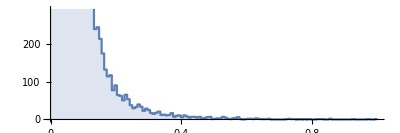

```mathematica
ImageHistogram[imEquM13, PlotRange->Automatic, Frame->False,Axes->True]
```

## Image Curves and Image Stretch

Typical ‘Photoshop’ astronomical workflow is to repeatedly apply the curve and levels tools.  We don’t have a ‘curves’ tool in Mathematica, but we can easily create a function which creates the same end effect:

```mathematica
CurveImage[x_, n_]:=(1-(x-1)^n)^(1/n)
```

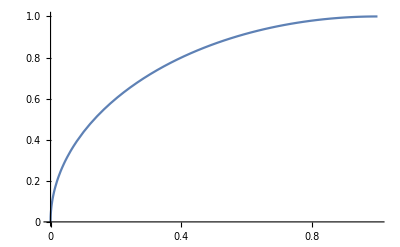

```mathematica
Plot[CurveImage[x,2],{x,0,1}]
```

In Photoshop, I use the ‘levels’ tool, to look for the lower limit of the peak in the histogram and then stretch from that point on to correspond to the interval {0.0,1.0}.  We can write a function which does the same thing in WL.

Here I find the lower limit of the peak as the location where the histogram is greater than the value a:

```mathematica
LevelImage[im_,a_]:=
Module[{min},
min=Select[ImageLevels[im],#[[2]]>a&][[1,1]];
ImageAdjust[im,{0.0,0.0},{min,1.0},{0.0,1.0}]
];
```

```mathematica
m13CurveAndStretch=CurveImage[LevelImage[imEquM13,2],2]
```

-Graphics-

#### Mild deconvolution to sharpen stars

```mathematica
m13Dec=ImageDeconvolve[m13CurveAndStretch,GaussianMatrix[2],Method->"RichardsonLucy"]
```

-Graphics-

#### Final stretch to darken background

```mathematica
m13Final=ImageAdjust[m13Dec,{.5,0.0}]
```

-Graphics-

```mathematica
Export["m13Final.png",m13Final]
```

m13Final.png

## Another example, using same dark, bias and flat frames

Galaxies NGC7331 and NGC7333

```mathematica
GalaxyData["NGC7331","Image"]
```

-Graphics-

```mathematica
targetName="NGC7333";
```

```mathematica
lightFiles= FileNames[FileNameJoin[{pictureLocation,targetName,"*.fit"}]];
outputFile=FileNameJoin[{pictureLocation,targetName<>".fit"}];
```

from astropy.io import fits
import astroalign as aa
import sys
import os
import numpy as np

np.random.seed(seed=12)

darkframe = <*darkFileName*>
print('dark frame: ' + darkframe)
hdul_dark = fits.open(darkframe)
data_dark = hdul_dark[0].data
hdul_dark.close()

biasframe = <*biasFileName*>
print('bias frame: ' + biasframe)
hdul_bias = fits.open(biasframe)
data_bias = hdul_bias[0].data
hdul_bias.close()

# Take the target for alignment to be the first of the light frames
targetframe = <*lightFiles*>[0]
print('target frame: ' + targetframe)
hdul_target = fits.open(targetframe)
data_target = hdul_target[0].data

# Calibrate the target frame
data_target -= data_dark # subtract out the dark noise
data_target -= data_bias # subtract out the read noise
newdata_target = data_target.byteswap().newbyteorder()
hdul_target.close()

image_concat = [] # empty list of aligned frames

print("Aligning " + str(len(<*lightFiles*>)) + " images")
for i in range(0, len(<*lightFiles*>)):
    hdul_im = fits.open(<*lightFiles*>[i])
    data_im = hdul_im[0].data # light frame data
    hdul_im.close()
    data_im -= data_dark # subtract out the dark noise
    data_im -= data_bias # subtract out the read noise

	# swap byte order from FITS big-endian to little-endian
	# so that little-endian based astroalign will work
    newdata_im = data_im.byteswap().newbyteorder() 

    # call the registration routine to align the frame with the key frame
    try:
        data_aligned, footprint = aa.register(newdata_im, newdata_target)
        image_concat.append(data_aligned) # add the aligned frame
    except aa.MaxIterError:
        print("Failed to align "+<*lightFiles*>[i]+" skipping...")

print("Stacking " + str(len(<*lightFiles*>)) + " images")
final_image = np.zeros(shape=image_concat[0].shape)

for image in image_concat:
        final_image += image

final_image = final_image / len(image_concat)
hdu = fits.PrimaryHDU(final_image)
print("Writing out stacked image: "+<*outputFile*>)
hdu.writeto(<*outputFile*>, overwrite=True)

dark frame: /Users/sherlock/Desktop/WTC2021/MasterDark.fit

bias frame: /Users/sherlock/Desktop/WTC2021/MasterBias.fit

target frame: /Users/sherlock/Desktop/WTC2021/NGC7333/9_17_21_NGC73311L60.fit

Aligning 6 images

Stacking 6 images

Writing out stacked image: /Users/sherlock/Desktop/WTC2021/NGC7333.fit

```mathematica
flatField = ImageAdjust@Import[flatFileName][1];
```

```mathematica
imAdjNGC7333=ImageAdjust@Import[outputFile][1];
```

```mathematica
imEquNGC7333=BrightnessEqualize[imAdjNGC7333,flatField]
```

-Graphics-

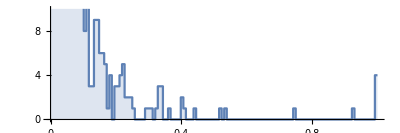

```mathematica
ImageHistogram[imEquNGC7333, PlotRange->Automatic, Frame->False,Axes->True]
```

```mathematica
ngc7333CurveAndStretch=CurveImage[LevelImage[imEquNGC7333,2],2]
```

-Graphics-

```mathematica
ngc7333Dec=ImageDeconvolve[ngc7333CurveAndStretch,GaussianMatrix[2],Method->"RichardsonLucy"]
```

-Graphics-

```mathematica
ImageAdjust[ngc7333Dec,{0.1,0.5}]
```

-Graphics-

After plate solving with external software (AllSkyPlateSolver):

## Conclusion

Mathematica can be successfully used in conjunction with Python to take advantage of many existing astronomical packages, that further enhance its already powerful image processing capabilities.

## Questions